```mathematica
((m-2)^2 α+m^2 γ)/Sqrt[α γ]
```

```mathematica
D[(((m-2)^2 α+m^2 γ)/Sqrt[α γ])^2-4 m^2(m-2)^2,m]
```

-8 (-2+m)^2 m-8 (-2+m) m^2+(2 (2 (-2+m) α+2 m γ) ((-2+m)^2 α+m^2 γ))/(α γ)

```mathematica
Solve[-8 (-2+m)^2 m-8 (-2+m) m^2+(2 (2 (-2+m) α+2 m γ) ((-2+m)^2 α+m^2 γ))/(α γ)==0,m]
```

```mathematica
{{m->(2 α)/(α-γ)},{m->2/(1+ (√γ)/(√α))+(2 (α-γ) β^2)/(√α (√α+√γ)^4 √γ)},{m->2/(1 -(√γ)/(√α))-(2 (α-γ) β^2)/(√α (√α-√γ)^4 √γ)}}
```

```mathematica
g[m_]:=((m-2)^2 α+m^2 γ)/Sqrt[α γ-β^2];
k2p[m_]:=(g[m]+Sqrt[(g[m])^2-4 m^2(m-2)^2])1/(2Sqrt[α γ-β^2]);
k2m[m_]:=(g[m]-Sqrt[(g[m])^2-4 m^2(m-2)^2])1/(2Sqrt[α γ-β^2]);
f[m_]:=g[m]^2-4 m^2(m-2)^2;
ξ2[m_]:= 1-2 β^2/(β^2+(α-m^2/k2[m])^2);
{k2pr,k2mr,k2pl,k2ml}->{4/(√α-√γ)^2+(4 β)/(√(α γ)(√α-√γ)^2)-(16 β^2)/(√α (√α-√γ)^4 √γ),4/(√α-√γ)^2-(4 β)/(√(α γ)(√α-√γ)^2)-(16 β^2)/(√α (√α-√γ)^4 √γ),4/(√α+√γ)^2+(4 β)/(√(α γ)(√α+√γ)^2)+(16 β^2)/(√α (√α+√γ)^4 √γ),4/(√α+√γ)^2-(4 β)/(√(α γ)(√α+√γ)^2)+(16 β^2)/(√α (√α+√γ)^4 √γ)};
```

```mathematica
{m31,m32,m33,m34}=n/.Solve[(k0^2/q^2(-2 β^2+2 α γ)-(n-2)^2 α-(n)^2 γ)^2==((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ),n];
```

```mathematica
{m31,m32,m33,m34}=n/.Solve[(k0^2/q^2(-2 β^2+2 α γ)-(n-2)^2 α-(n)^2 γ)^2==((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)/.β->0,n]
```

```mathematica
{{n->1/2 √(k0^2 α) (-2-(k0^2 β^2)/(α (4+4 √(k0^2 α)+k0^2 (α-γ))))},{n->1/2 √(k0^2 α) (2+(k0^2 β^2)/(α (4-4 √(k0^2 α)+k0^2 (α-γ))))},{n->2-√(k0^2 γ)+(k0^4 β^2)/(2 √(k0^2 γ) (-4+k0^2 (α-γ)+4 √(k0^2 γ)))},{n->2+√(k0^2 γ)+(k0^4 β^2)/(2 √(k0^2 γ) (k0^2 (-α+γ)+4 (1+√(k0^2 γ))))}}
```

```mathematica
(4+4 k0 √α+k0^2 (α-γ))-((k0 √α+2)^2-γ k0^2 )//Simplify
```

0

```mathematica
(*инициализация*)
```

```mathematica
q=1;
bl={inp,inm,hp,hm};
gg=xr/Sqrt[2]{0,2,0,k0/q 2}+xl/Sqrt[2]{2,0,k0/q 2,0};
{m31,m32,m33,m34}={-(k0 √α)/q,(k0 √α)/q,(2 q-k0 √γ)/q,(2 q+k0 √γ)/q};
m=Assuming[k0>0,{m1-> 1/2 √(k0^2 α) (-2-(k0^2 β^2)/(α (4+4 √(k0^2 α)+k0^2 (α-γ)))),m2->1/2 √(k0^2 α) (2+(k0^2 β^2)/(α (4-4 √(k0^2 α)+k0^2 (α-γ)))),m3-> 2-√(k0^2 γ)+(k0^4 β^2)/(2 √(k0^2 γ) (-4+k0^2 (α-γ)+4 √(k0^2 γ))),m4-> 2+√(k0^2 γ)+(k0^4 β^2)/(2 √(k0^2 γ) (k0^2 (-α+γ)+4 (1+√(k0^2 γ))))}//Simplify];
m0=Assuming[k0>0,{m1-> 1/2 √(k0^2 α) (-2-(k0^2 β^2)/(α (4+4 √(k0^2 α)+k0^2 (α-γ)))),m2->1/2 √(k0^2 α) (2+(k0^2 β^2)/(α (4-4 √(k0^2 α)+k0^2 (α-γ)))),m3-> 2-√(k0^2 γ)+(k0^4 β^2)/(2 √(k0^2 γ) (-4+k0^2 (α-γ)+4 √(k0^2 γ))),m4-> 2+√(k0^2 γ)+(k0^4 β^2)/(2 √(k0^2 γ) (k0^2 (-α+γ)+4 (1+√(k0^2 γ))))}/.β-> 0//Simplify];
(*{m31,m32,m33,m34}={-(k0 √α)/q+δm1 β^2,(k0 √α)/q+δm2 β^2,(2 q-k0 √γ)/q+δm3 β^2,(2 q+k0 √γ)/q+δm4 β^2};*)
t={t1-> (m1^2 -α k0^2)/(β k0^2),t2-> (m2^2 -α k0^2)/(β k0^2),t3-> (m3^2 -α k0^2)/(β k0^2),t4-> (m4^2 -α k0^2)/(β k0^2)};
U[z_]:={{ⅇ^(ⅈ m31 q z),ⅇ^(ⅈ m32 q z),ⅇ^(ⅈ m33 q z),ⅇ^(ⅈ m34 q z)},
{t1 ⅇ^(ⅈ m31 q z),t2 ⅇ^(ⅈ m32 q z),t3 ⅇ^(ⅈ m33 q z),t4 ⅇ^(ⅈ m34 q z)},
{m1  ⅇ^(ⅈ m31 q z),m2  ⅇ^(ⅈ m32 q z),m3  ⅇ^(ⅈ m33 q z) ,m4  ⅇ^(ⅈ m34 q z) },
{t1 m1  ⅇ^(ⅈ m31 q z),t2 m2  ⅇ^(ⅈ m32 q z),t3 m3  ⅇ^(ⅈ m33 q z) ,t4 m4  ⅇ^(ⅈ m34 q z) }};
U0=1/Sqrt[2]{{0,2,-2,0},{2,0,0,-2},{0,2 k0/q,2 k0/q,0},{2 k0/q,0,0,2 k0/q}};
T={{ⅇ^(-ⅈ k0 L),0,0,0},{0,ⅇ^(-ⅈ k0 L),0,0},{0,0,ⅇ^(-ⅈ k0 L),0},{0,0,0,ⅇ^(-ⅈ k0 L)}};
b={b1,b2,b3,b4};
U[-L].b ==U0.T.bl;
U[0].b==gg;
```

```mathematica
Clear[m34]
```

```mathematica
(*!рабочее решение для правой поляризации (нужно учитывать более высокие порядки почти до конца)*)
prms={inp->1,inm-> 0};
expr= U[-L].b - U0.T.bl /.t/.prms//Simplify;
mid0=Solve[expr==0,{b1,b2,b3,b4}]/.prms//Simplify;
tmp=b/.mid0;
tmp1=Series[tmp/.m,{β,0,2}]/.prms//Simplify//Normal;
fin=U[0].tmp1[[1]]==gg/.t/.m/.prms//Simplify;finsol=Solve[fin,{xr,xl,hp,hm}];
```

```mathematica
kk={xr,xl,hp,hm}/.finsol/.m(*/.k0-> 2/(√α-√γ)+Δ β*)/.prms;
Series[kk,{β,0,1}]//Normal//Simplify//FullSimplify
```

{{-(4 ⅇ^(ⅈ L (2+k0 (-1+√γ))) k0^2 √γ)/(4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2),(4 k0^2 β (-ⅇ^(ⅈ k0 L (-1+√α+2 √γ)) √α (-4+k0^2 (-1+√γ)^2) (-4+k0^2 (α-γ)-4 k0 √γ)+ⅇ^(ⅈ k0 L (-1+√α)) √α (-4+k0^2 (1+√γ)^2) (-4+k0^2 (α-γ)+4 k0 √γ)+ⅇ^(ⅈ L (2+k0 (-1+2 √α+√γ))) k0 (4+k0 (-1+√α)) (-1+√α) √γ ((-2+k0 √α)^2-k0^2 γ)+ⅇ^(ⅈ L (2+k0 (-1+√γ))) k0 (1+√α) (-4+k0+k0 √α) √γ (-(2+k0 √α)^2+k0^2 γ)))/((ⅇ^(2 ⅈ k0 L √α) (-1+√α)^2-(1+√α)^2) (-2+k0 (√α-√γ)) (2+k0 (√α-√γ)) (4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2) (-2+k0 (√α+√γ)) (2+k0 (√α+√γ))),-((2 k0^2 β (ⅇ^(2 ⅈ k0 L (√α+√γ)) (-1+√α) (-2+k0 (√α-√γ)) (2+k0 (√α-√γ)) (2+k0 (-1+√γ)) (2+k0 (√α+√γ))+ⅇ^(2 ⅈ k0 L √γ) (1+√α) (2+k0 (-1+√γ)) (2+k0 (-√α+√γ)) (-2+k0 (√α+√γ)) (2+k0 (√α+√γ))-(1+√α) (-2+k0 (√α-√γ)) (2+k0 (√α-√γ)) (-2+k0 (√α+√γ)) (-2+k0+k0 √γ)+ⅇ^(2 ⅈ k0 L √α) (-1+√α) (2+k0 (√α-√γ)) (-2+k0 (√α+√γ)) (2+k0 (√α+√γ)) (-2+k0+k0 √γ)-16 ⅇ^(ⅈ L (2+k0 (√α+√γ))) k0 √α (-4+k0 (4+k0 (-1+γ))) √γ))/((ⅇ^(2 ⅈ k0 L √α) (-1+√α)^2-(1+√α)^2) (-2+k0 (√α-√γ)) (2+k0 (√α-√γ)) (4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2) (-2+k0 (√α+√γ)) (2+k0 (√α+√γ)))),((-1+ⅇ^(2 ⅈ k0 L √γ)) (-4+k0 (4+k0 (-1+γ))))/(4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2)}}

```mathematica
{-(4 ⅇ^(ⅈ L (2-2 k0/km)) k0^2 √γ)/(4-4 k0^2/kp^2-ⅇ^(2 ⅈ k0 L √γ) (4-4 k0^2/km^2 )),(k0^2 β (ⅇ^(2 ⅈ k0 L √γ) (1-k0/km )^2-(1-k0/kp)^2+ ⅇ^(ⅈ L (2-2 k0/km )) (-2+k0) k0 √γ))/(4(1-k0/km )(1-k0/kp ) (1-k0^2/kp^2-ⅇ^(2 ⅈ k0 L √γ) (1-k0^2/km^2 ) )),(k0^2 β (k0^2/(kp km) -1+ⅇ^(2 ⅈ k0 L √γ) (1-k0^2/(kp km) + k0 √γ)+ k0 √γ(1-2 ⅇ^(ⅈ L (2+2 k0/kp)))))/(4(1+k0/km )(1+k0/kp) (-1+k0^2/kp^2+ⅇ^(2 ⅈ k0 L √γ) (1-k0^2/km^2 ) )),((-1+ⅇ^(2 ⅈ k0 L √γ)) (-4+4 k0-(4 k0^2)/(km kp)))/(4-4 k0^2/kp^2+ⅇ^(2 ⅈ k0 L √γ) (-4+4 k0^2/km^2))}
```

Power::infy: Infinite expression 1/0 encountered.

{1,ComplexInfinity,-1/4 (-1+ⅇ^((4 ⅈ L)/(1+√γ))) β,0}

```mathematica
(*!рабочее решение для левой поляризации (нужно учитывать более высокие порядки почти до конца)*)
prms={inp->0,inm-> 1};
expr= U[-L].b - U0.T.bl /.t/.prms//Simplify;
mid0=Solve[expr==0,{b1,b2,b3,b4}]/.prms//Simplify;
tmp=b/.mid0;
tmp1=Series[tmp/.m,{β,0,2}]/.prms//Simplify//Normal;
fin=U[0].tmp1[[1]]==gg/.t/.m/.prms//Simplify;finsol=Solve[fin,{xr,xl,hp,hm}];
```

```mathematica
kk={xr,xl,hp,hm}/.finsol/.m(*/.k0-> 2/(√α-√γ)+Δ β*)/.prms;
Series[kk,{β,0,1}]//Normal//Simplify//FullSimplify
```

{{(4 k0^2 β (-ⅇ^(ⅈ k0 L (-1+√α+2 √γ)) √α (-4+k0^2 (α-γ)-4 k0 √γ) (2+k0-k0 √γ)^2+ⅇ^(ⅈ k0 L (-1+√α)) √α (2+k0+k0 √γ)^2 (-4+k0^2 (α-γ)+4 k0 √γ)+ⅇ^(ⅈ L (2+k0 (-1+2 √α+√γ))) k0^2 (-1+√α)^2 √γ ((-2+k0 √α)^2-k0^2 γ)+ⅇ^(ⅈ L (2+k0 (-1+√γ))) k0^2 (1+√α)^2 √γ (-(2+k0 √α)^2+k0^2 γ)))/((ⅇ^(2 ⅈ k0 L √α) (-1+√α)^2-(1+√α)^2) (-2+k0 (√α-√γ)) (2+k0 (√α-√γ)) (4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2) (-2+k0 (√α+√γ)) (2+k0 (√α+√γ))),(2 ⅈ ⅇ^(-ⅈ k0 L) √α)/(2 ⅈ √α Cos[k0 L √α]+(1+α) Sin[k0 L √α]),((-1+α) Sin[k0 L √α])/(2 ⅈ √α Cos[k0 L √α]+(1+α) Sin[k0 L √α]),-((2 k0^2 β (ⅇ^(2 ⅈ k0 L (√α+√γ)) (-1+√α) (-2+k0 (√α-√γ)) (2+k0 (√α-√γ)) (2+k0 (-1+√γ)) (-2+k0 (√α+√γ))+ⅇ^(2 ⅈ k0 L √γ) (1+√α) (2+k0 (-1+√γ)) (-2+k0 (-√α+√γ)) (-2+k0 (√α+√γ)) (2+k0 (√α+√γ))-(1+√α) (-2+k0 (√α-√γ)) (2+k0 (√α-√γ)) (2+k0 (√α+√γ)) (-2+k0+k0 √γ)+ⅇ^(2 ⅈ k0 L √α) (-1+√α) (-2+k0 (√α-√γ)) (-2+k0 (√α+√γ)) (2+k0 (√α+√γ)) (-2+k0+k0 √γ)+16 ⅇ^(ⅈ L (-2+k0 (√α+√γ))) k0^3 (-1+α) √α √γ))/((ⅇ^(2 ⅈ k0 L √α) (-1+√α)^2-(1+√α)^2) (-2+k0 (√α-√γ)) (2+k0 (√α-√γ)) (4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2) (-2+k0 (√α+√γ)) (2+k0 (√α+√γ))))}}

```mathematica
{(k0^2 β (1-k0^2/kp^2-ⅇ^(2 ⅈ k0 L √γ) (1-k0^2/km^2 ) + ⅇ^(ⅈ L (2-2 k0/km )) k0^2 √γ))/(4(1-k0/km )(1-k0/kp) (1-k0^2/kp^2-ⅇ^(2 ⅈ k0 L √γ) (1-k0^2/km^2 ) )),1,0,((-1+ⅇ^(2 ⅈ k0 L √γ)) k0^2 β)/(4-4 k0^2/kp^2 -ⅇ^(2 ⅈ k0 L √γ) (4-4 k0^2/km^2 ))}/.β-> 0
```

{0,1,0,0}

```mathematica
((-1+ⅇ^(2 ⅈ k0 L √γ)) k0^2 β)/(4-4 k0^2/kp^2 -ⅇ^(2 ⅈ k0 L √γ) (4-4 k0^2/km^2 ))*((-1+ⅇ^(-2 ⅈ k0 L √γ)) k0^2 β)/(4-4 k0^2/kp^2 -ⅇ^(-2 ⅈ k0 L √γ) (4-4 k0^2/km^2 ))/.km-> 2/(1-√γ)/.kp-> 2/(1+√γ)//Simplify
```

((-1+ⅇ^(2 ⅈ k0 L √γ))^2 k0^4 β^2)/((4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (1+√γ)^2)-k0^2 (-1+√γ)^2) (4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2))

```mathematica
Limit[((-1+ⅇ^(2 ⅈ k0 L √γ))^2 k0^4 β^2)/((4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (1+√γ)^2)-k0^2 (-1+√γ)^2) (4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2)),k0-> 2/(1-√γ)]//Simplify
```

-(ⅇ^(-(4 ⅈ L √γ)/(-1+√γ)) (-1+ⅇ^((4 ⅈ L √γ)/(-1+√γ)))^2 β^2)/(16 γ)

```mathematica
ExpToTrig[-(ⅇ^(-(4 ⅈ L √γ)/(-1+√γ)) (-1+ⅇ^((4 ⅈ L √γ)/(-1+√γ)))^2 β^2)/(16 γ)]//Expand//Simplify
```

(β^2 Sin[(2 L √γ)/(-1+√γ)]^2)/(4 γ)

```mathematica
fk0T[α_,γ_,β_,{inp_,inm_},L_,dRange_]:=Module[{xr,xl,hp,hm,xi2Trans,xi1Trans,xi3Trans,trans,r},
{xr,xl,hp,hm}={(k0^2 β (4-4 k0^2/kp^2-ⅇ^(2 ⅈ k0 L √γ) (4-4 k0^2/km^2 ) +4 ⅇ^(ⅈ L (2-2 k0/km )) k0^2 √γ))/((2-2 k0/km ) (4-ⅇ^(2 ⅈ k0 L √γ) (4-4 k0^2/km^2 )-4 k0^2/kp^2 ) (2-2 k0/kp)),1,0,((-1+ⅇ^(2 ⅈ k0 L √γ)) k0^2 β)/(4-4 k0^2/kp^2 -ⅇ^(2 ⅈ k0 L √γ) (4-4 k0^2/km^2 ))}inm+{-(4 ⅇ^(ⅈ L (2-2 k0/km)) k0^2 √γ)/(4-4 k0^2/kp^2-ⅇ^(2 ⅈ k0 L √γ) (4-4 k0^2/km^2 )),(k0^2 β (ⅇ^(2 ⅈ k0 L √γ) (2-2 k0/km )^2-(2-2 k0/kp)^2+4 ⅇ^(ⅈ L (2-2 k0/km )) (-2+k0) k0 √γ))/((2-2 k0/km )(2-2 k0/kp ) (4-4 k0^2/kp^2-ⅇ^(2 ⅈ k0 L √γ) (4-4 k0^2/km^2 ) )),(k0^2 β (-4+ⅇ^(2 ⅈ k0 L √γ) (4-4 k0^2/(kp km) +4 k0 √γ)+4 k0^2/(kp km) +4 k0 √γ(1-2 ⅇ^(ⅈ L (2+2 k0/kp)))))/((-2-2 k0/km ) (4-4 k0^2/kp^2+ⅇ^(2 ⅈ k0 L √γ) (-4+4 k0^2/km^2 ) ) (2+2 k0/kp)),((-1+ⅇ^(2 ⅈ k0 L √γ)) (-4+4 k0-(4 k0^2)/(km kp)))/(4-4 k0^2/kp^2+ⅇ^(2 ⅈ k0 L √γ) (-4+4 k0^2/km^2))}inp/.km-> 2/(1-√γ)/.kp-> 2/(1+√γ);
xi2Trans=(Abs[xr]^2-Abs[xl]^2)/(Abs[xl]^2+Abs[xr]^2);
xi1Trans=(xl*Conjugate[xr]-Conjugate[xl]*xr)/(ⅈ(Abs[xl]^2+Abs[xr]^2));
xi3Trans=(xl*Conjugate[xr]+Conjugate[xl]*xr)/(Abs[xl]^2+Abs[xr]^2);
trans=(Abs[xl]^2+Abs[xr]^2)/(Abs[inp]^2+Abs[inm]^2);

r={Plot[trans,{k0, 1,8},PlotRange->All,AxesLabel-> {"Δ",None},PlotLabel->"коэф прохождения"],
Plot[{xi1Trans,xi2Trans,xi3Trans},{δ, -dRange, dRange},PlotRange->All,AxesLabel-> {"Δ",None},PlotLabel->"Все Стокс пр. волны"],
Plot[xi1Trans,{k0, 1,8},PlotRange->All,AxesLabel-> {"Δ",None},PlotLabel->"1 Стокс пр. волны"],
Plot[xi2Trans,{k0,1,8},PlotRange->All,AxesLabel-> {"Δ",None},PlotLabel->"2 Стокс пр. волны",PlotStyle->Orange],Plot[xi3Trans,{k0, 1,8},PlotRange->All,AxesLabel-> {"Δ",None},PlotLabel->"2 Стокс пр. волны",PlotStyle->Green]};
r
]
```

```mathematica
fk0[α_,γ_,β0_,{inp_,inm_},L_,dRange_]:=Module[{xr,xl,hp,hm,xi2Trans,xi1Trans,xi3Trans,trans,r,β},
{xr,xl,hp,hm}={-(k0^2 β (4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2+4 ⅇ^(ⅈ L (2+k0 (-1+√γ))) k0^2 √γ))/((2+k0 (-1+√γ)) (4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2) (-2+k0+k0 √γ)),1,0,((-1+ⅇ^(2 ⅈ k0 L √γ)) k0^2 β)/(4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2)}inm+{-(4 ⅇ^(ⅈ L (2+k0 (-1+√γ))) k0^2 √γ)/(4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2),-(k0^2 β (ⅇ^(2 ⅈ k0 L √γ) (2+k0 (-1+√γ))^2-(-2+k0+k0 √γ)^2+4 ⅇ^(ⅈ L (2+k0 (-1+√γ))) (-2+k0) k0 √γ))/((2+k0 (-1+√γ)) (4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2) (-2+k0+k0 √γ)),(k0^2 β (-4+ⅇ^(2 ⅈ k0 L √γ) (4+k0^2 (-1+γ)+4 k0 √γ)-8 ⅇ^(ⅈ L (2+k0+k0 √γ)) k0 √γ+k0 (k0+4 √γ-k0 γ)))/((-2+k0 (-1+√γ)) (4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2) (2+k0+k0 √γ)),((-1+ⅇ^(2 ⅈ k0 L √γ)) (-4+k0 (4+k0 (-1+γ))))/(4+ⅇ^(2 ⅈ k0 L √γ) (-4+k0^2 (-1+√γ)^2)-k0^2 (1+√γ)^2)}inp;
xi2Trans=(Abs[xr]^2-Abs[xl]^2)/(Abs[xl]^2+Abs[xr]^2);
xi1Trans=(xl*Conjugate[xr]-Conjugate[xl]*xr)/(ⅈ(Abs[xl]^2+Abs[xr]^2));
xi3Trans=(xl*Conjugate[xr]+Conjugate[xl]*xr)/(Abs[xl]^2+Abs[xr]^2);
trans=(Abs[xl]^2+Abs[xr]^2)/(Abs[inp]^2+Abs[inm]^2);
β=β0;
r={Plot[trans,{k0, 1,8},PlotRange->All,AxesLabel-> {"Δ",None},PlotLabel->"коэф прохождения"],
Plot[{xi1Trans,xi2Trans,xi3Trans},{δ, -dRange, dRange},PlotRange->All,AxesLabel-> {"Δ",None},PlotLabel->"Все Стокс пр. волны"],
Plot[xi1Trans,{k0, 1,8},PlotRange->All,AxesLabel-> {"Δ",None},PlotLabel->"1 Стокс пр. волны"],
Plot[xi2Trans,{k0,1,8},PlotRange->All,AxesLabel-> {"Δ",None},PlotLabel->"2 Стокс пр. волны",PlotStyle->Orange],Plot[xi3Trans,{k0, 1,8},PlotRange->All,AxesLabel-> {"Δ",None},PlotLabel->"2 Стокс пр. волны",PlotStyle->Green]};
r
]
```

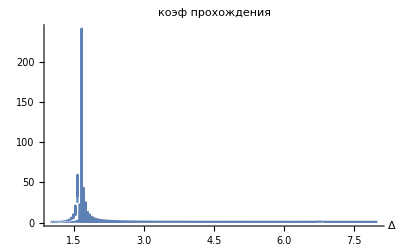
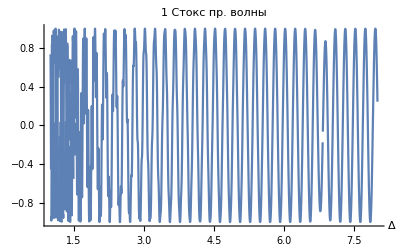
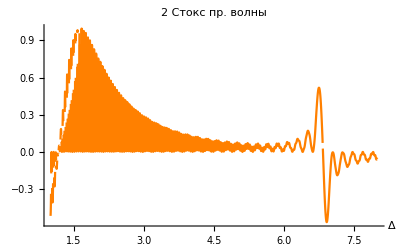
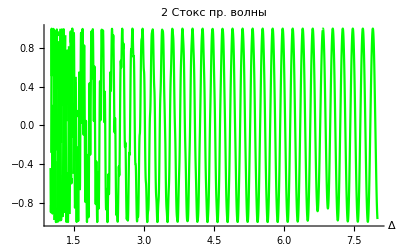
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fk0[1,0.5,0.001,{1,1},100,0.1]
```

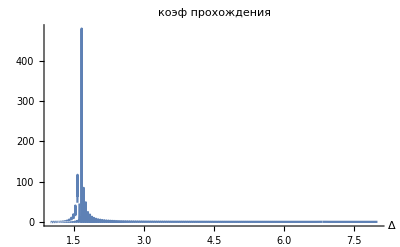
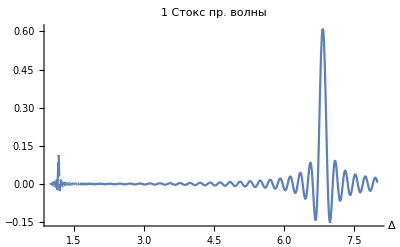
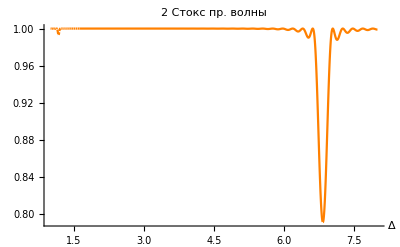
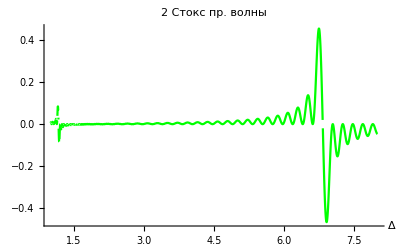
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fk0T[1,0.5,0.001,{1,0},100,0.1]
```